# Why not Galerkin here?

```mathematica
a=0;
b=3;
H[fx_]:=∫_a^b fxⅆx;
ϕ1=x;
ϕ2=x^2;
ϕ3=x^3;
f=x^3 ⅇ^x;
A={
{H[ϕ1 D[ϕ1, x]],H[ϕ1 D[ϕ2, x]],H[ϕ1 D[ϕ3, x]]},
{H[ϕ2 D[ϕ1, x]],H[ϕ2 D[ϕ2, x]],H[ϕ2 D[ϕ3, x]]},
{H[ϕ3 D[ϕ1, x]],H[ϕ3 D[ϕ2, x]],H[ϕ3 D[ϕ3, x]]}
}//FullSimplify;
b={H[ϕ1 f], H[ϕ2 f],H[ϕ3 f]}//FullSimplify;
{a1,a2,a3}=Dot[Inverse[A],b]//FullSimplify;
A
b
a1
a2
a3
```

{{9/2,18,243/4},{9,81/2,729/5},{81/4,486/5,729/2}}

{-24+33 ⅇ^3,120+78 ⅇ^3,9 (-80+29 ⅇ^3)}

4/3 (-2144+113 ⅇ^3)

20 (92-5 ⅇ^3)

20/81 (-1352+77 ⅇ^3)

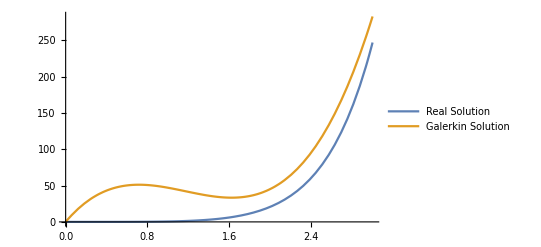

```mathematica
yy=a1 x+a2 x^2+a3 x^3;
y=∫_0^x t^3 ⅇ^t ⅆt//FullSimplify;
Plot[{y,yy},{x,0,3},PlotLegends->{"Real Solution","Galerkin Solution"}]
```